```mathematica
files=FileNames["*.tab"];
datas=Drop[Import[#],1]&/@files;
ch1s=Transpose[{#[[All,1]],#[[All,2]]}]&/@datas;
ch2s=Transpose[{#[[All,1]],#[[All,3]]}]&/@datas;
data=Transpose[{ch1s,ch2s}];
```

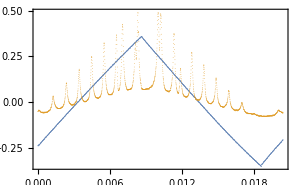
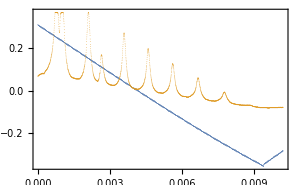
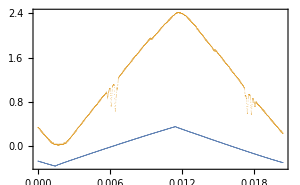
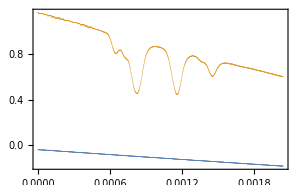
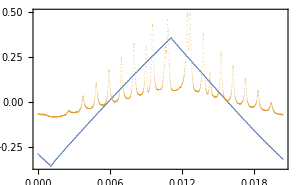
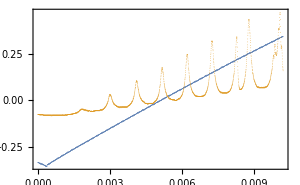
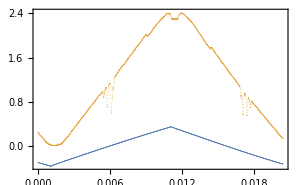
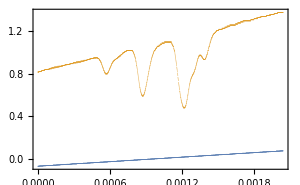

```mathematica
ListPlot[#, PlotRange->All, Frame->True, ImageSize->300, PlotStyle->{PointSize[0.0001]}]&/@ data
```

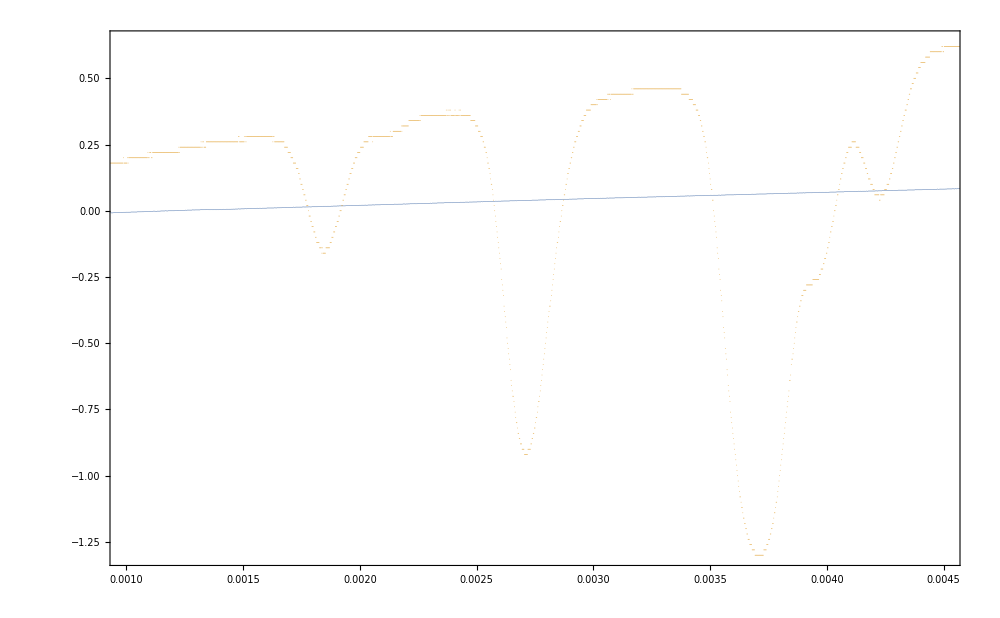

```mathematica
ListPlot[data[[9]], PlotRange->{{0.001, 0.0045}, All}, Frame->True, ImageSize->1000, PlotStyle->{PointSize[0.0001]}]
```

```mathematica
params ={{0.002164,0.3541},{0.002254,-0.4825},{0.00234,0.2603}};
A = Mean[{params[[2, 2]] -params[[1, 2]], params[[2, 2]] - params[[3, 2]] }];
c = params[[2, 1]];
σ = Abs[Mean[{params[[2, 1]] -params[[1, 1]], params[[2, 1]] - params[[3, 1]] }]];
{A, c, σ *10^6}
```

{-0.7897,0.002254,2.}

```mathematica
xminmax = {{0.001092,0.5004},{0.001582,0.3428}};
Transpose[xminmax][[1]]
```

{0.001092,0.001582}